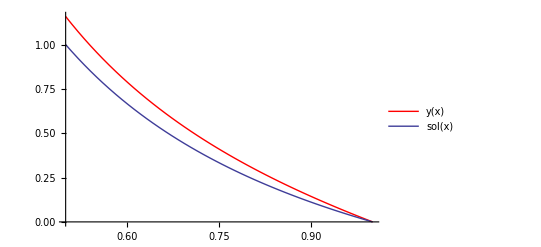

Погрешность приближения равна: 0.0387955

```mathematica
(*Зададим коэффициенты данного дифференциального уравнения*)
p[x_]=-1/x;
q[x_]=-3/x^2;
f[x_]=3/x^2;
(*Зададим краевые условия*)
a=1/2;
alpha0=1;
alpha1=1/2;
A=-1;
b=1;
beta0=1;
beta1=0;
B=0;
(*Зададим количество частичных отрезков*)
n=50;
(*Найдем шаг разбиения*)
h=(b-a)/n;
(*Построим разбиение отрезка на частичные*)
X=Table[a+k*h,{k,0,n}];
(*Зададим сеточные функции коэффициентов и свободного члена дифференциального уравнения*)
P=Table[p[X[[k]]],{k,1,n+1}];
Q=Table[q[X[[k]]],{k,1,n+1}];
F=Table[f[X[[k]]],{k,1,n+1}];
(*Составим основную матрицу системы уравнений для поиска каркаса решения*)
M=Table[0,{i,1,n+1},{j,1,n+1}];
k=2;
For[i=2,i≤n,i++,
M[[i,k-1]]=1-h/2*P[[k]];
M[[i,k]]=h^2*Q[[k]]-2;
M[[i,k+1]]=1+h/2*P[[k]];
k=k+1
];
M[[1,1]]=alpha0*h-alpha1;
M[[1,2]]=alpha1;
M[[n+1,n]]=beta1;
M[[n+1,n+1]]=-(beta1+h*beta0);
(*Зададим столбец свободных членов системы для поиска каркаса решения*)
S=Table[h^2*F[[k]],{k,2,n}];
PrependTo[S,h*A];
AppendTo[S,-h*B];
(*Найдем каркас решения методом обратной матрицы*)
Y=Inverse[M].S;
(*Выполним интерполяцию полученного приближенного решения многочленом Лагранжа*)
y[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Найдем точное решение данной задачи*)
Sol=DSolve[{s''[x]+p[x]*s'[x]+q[x]*s[x]==f[x],alpha0*s[a]+alpha1*s'[a]==A,beta0*s[b]+beta1*s'[b]==B},s[x],x];
sol[x_]=s[x]/.Sol[[1]];
(*Построим графики приближенного и точного решения в одной системе координат*)
GR=Plot[y[x],{x,a,b},PlotStyle->Red,PlotLegends->"Expressions"];
G=Plot[sol[x],{x,a,b},PlotLegends->"Expressions"];
Show[GR,G]
(*Найдем погрешность приближения*)
r=NIntegrate[Abs[y[x]-sol[x]],{x,a,b}];
Print["Погрешность приближения равна: ",r]
```